```mathematica
Simplify@D[4ϵ((σ/r)^12-(σ/r)^6),r]
```

(24 ϵ σ^6 (r^6-2 σ^6))/r^13

-Graphics3D-

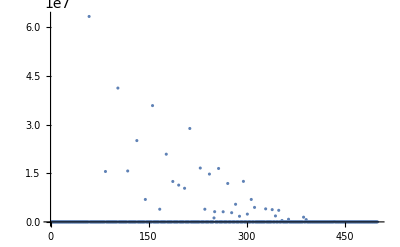

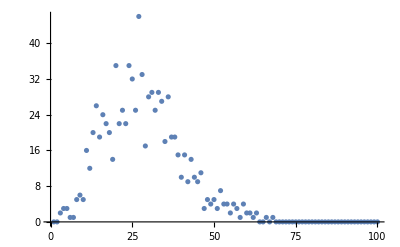

-Graphics-

-Graphics-

```mathematica
scaleFactor=10^0;
initPositions= ReadList["~/phd-stuff/courses/astrid_sim/positions.txt",Number,RecordLists->True]*scaleFactor;
ListPointPlot3D[initPositions,BoxRatios->{1, 1, 1},AxesLabel->{"x","y","z"}]
velocities= ReadList["~/phd-stuff/courses/astrid_sim/velocities.txt",Number,RecordLists->False];
sortvelocities=Sort[Flatten@velocities];
rdf= ReadList["~/phd-stuff/courses/astrid_sim/radialdistfunc.txt",Number,RecordLists->False];
ListPlot[rdf]
veldist = ReadList["~/phd-stuff/courses/astrid_sim/speeddist.txt",Number,RecordLists->False];
ListPlot[veldist]
```

```mathematica
initPositions
SortBy[initPositions,#[[3]]&];numvel=Table[{k,velocities[[k]]},{k,1,Length[velocities]}];
Sort[numvel,#1[[2]]>#2[[2]]&];
```

```mathematica
initPositions[[1]]
initPositions[[2]]
initPositions[[3]]
initPositions[[4]]
initPositions[[5]]
initPositions[[6]]
```

{2.47836×10^-9,2.47836×10^-9,2.47836×10^-9}

{10,10,10}

{9.95028×10^-24,-3.81431×10^-25}

{3.47736×10^-9,3.47736×10^-9,3.47736×10^-9}

{-10,-10,-10}

{9.95028×10^-24,-3.81431×10^-25}

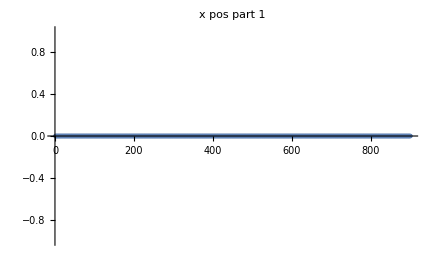

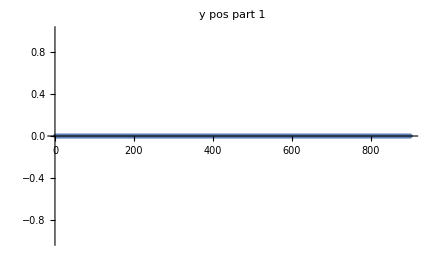

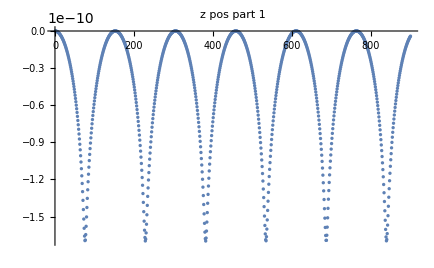

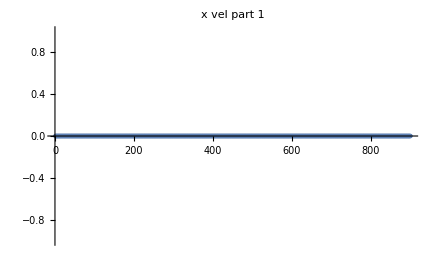

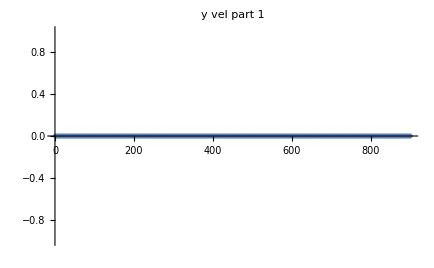

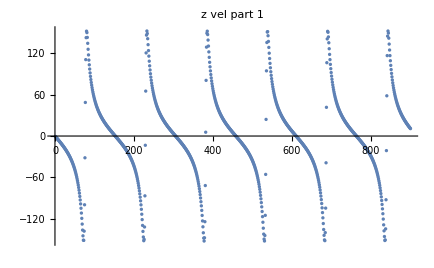

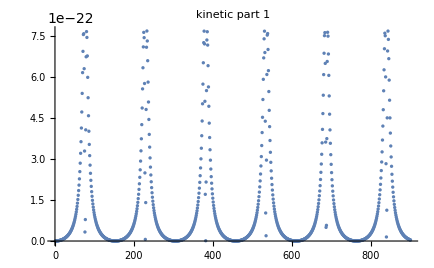

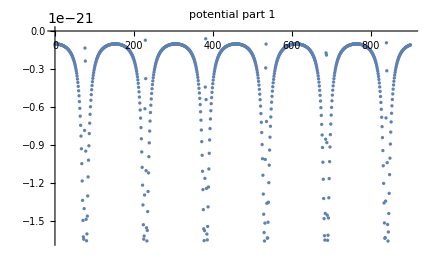

```mathematica
scaleFactor=10^0;
initPositions= ReadList["~/phd-stuff/courses/astrid_sim/testpositions.txt",Number,RecordLists->True]*scaleFactor;
pos11=Table[initPositions[[1+6i]][[1]],{i,0,900}];
pos12=Table[initPositions[[1+6i]][[2]],{i,0,900}];
pos13=Table[initPositions[[1+6i]][[3]],{i,0,900}];
vel11=Table[initPositions[[2+6i]][[1]]  ,{i,0,900}];
vel12=Table[initPositions[[2+6i]][[2]]  ,{i,0,900}];
vel13=Table[initPositions[[2+6i]][[3]]  ,{i,0,900}];
kin1 = Table[initPositions[[3+6i]][[1]],{i,0,900}];
pot1= Table[initPositions[[3+6i]][[2]],{i,0,900}];
pos21=Table[initPositions[[4+6i]][[1]],{i,0,900}];
vel21=Table[initPositions[[5+6i]][[1]],{i,0,900}];
kin2 = Table[initPositions[[0+6i]][[1]],{i,1,900}];
pot2= Table[initPositions[[0+6i]][[2]],{i,1,900}];

ListPlot[pos11,PlotLabel->"x pos part 1"]
ListPlot[pos12,PlotLabel->"y pos part 1"]
ListPlot[pos13,PlotLabel->"z pos part 1"]
ListPlot[vel11,PlotLabel->"x vel part 1"]
ListPlot[vel12,PlotLabel->"y vel part 1"]
ListPlot[vel13,PlotLabel->"z vel part 1"]
ListPlot[kin1,PlotLabel->"kinetic part 1"]
ListPlot[pot1,PlotLabel->"potential part 1"]
ListPlot[kin1-pot1,PlotLabel->"energy conservation"]
```

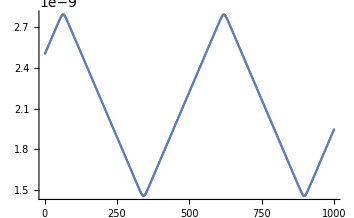

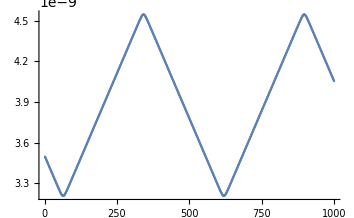

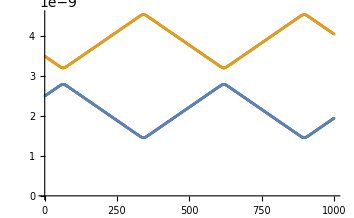

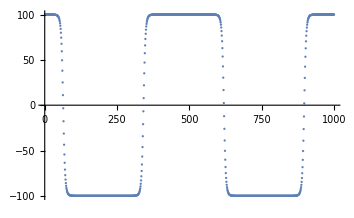

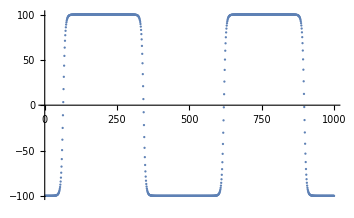

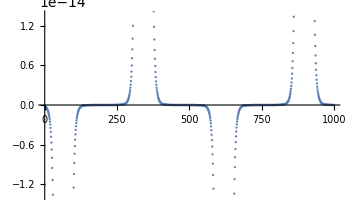

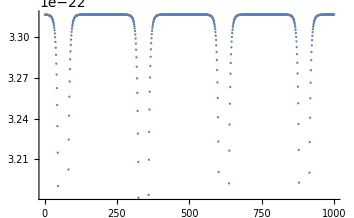

-Graphics-

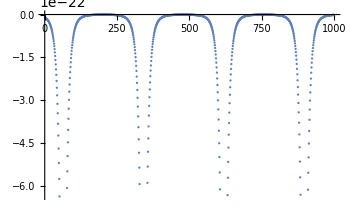

-Graphics-

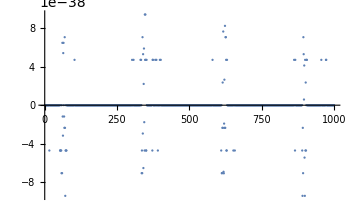

```mathematica
verlet= ReadList["~/phd-stuff/courses/astrid_sim/periodicverlet.txt",Number,RecordLists->True];

xpos=Table[verlet[[1+4*i]][[1]],{i,0,Length[(verlet)]/4-1}];
v=Table[verlet[[1+4*i]][[2]],{i,0,Length[(verlet)]/4-1}];
kin=Table[verlet[[1+4*i]][[3]],{i,0,Length[(verlet)]/4-1}];
pot=Table[verlet[[1+4*i]][[4]],{i,0,Length[(verlet)]/4-1}];
force=Table[verlet[[4+4*i]][[1]],{i,0,Length[(verlet)]/4-1}];

xpos2=Table[verlet[[2+4*i]][[1]],{i,0,Length[(verlet)]/4-1}];
v2=Table[verlet[[2+4*i]][[2]],{i,0,Length[(verlet)]/4-1}];
kin2=Table[verlet[[2+4*i]][[3]],{i,0,Length[(verlet)]/4-1}];
pot2=Table[verlet[[2+4*i]][[4]],{i,0,Length[(verlet)]/4-1}];

ListPlot[{xpos}]
ListPlot[{xpos2}]

ListPlot[{xpos,xpos2}]

ListPlot[{v}]
ListPlot[{v2}]

ListPlot[force]

ListPlot[{kin}]
ListPlot[{kin2}]

ListPlot[{pot}]
ListPlot[{pot2}]

ListPlot[{kin+pot-(kin2+pot2)}]

k=650;
xpos[[k]];
xpos2[[k]];
```

4 ϵ (-σ^6/r^6+σ^12/r^12)

-4 ϵ ((6 σ^6)/r^7-(12 σ^12)/r^13)

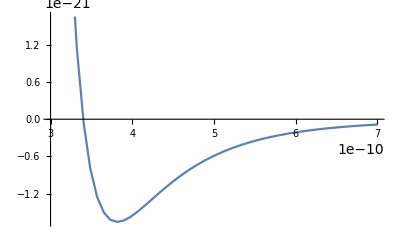

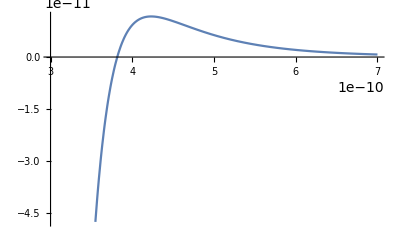

```mathematica
T=120;
sigma=3.4*^-10;
kB=1.38064852*^-23;
epsilon=T*kB;
umass=1.660539040*^-27;
argonmass=umass*39.948;

min = 3*^-10;
max = 7*^-10;

4*ϵ*((σ/r)^12-(σ/r)^6)
-D[%,r]

Plot[4*epsilon*((sigma/r)^12-(sigma/r)^6),{r,min,max}]
Plot[4 epsilon ((6 sigma^6)/r^7-(12 sigma^12)/r^13),{r,min,max}]

Manipulate[4*epsilon*((sigma/r)^12-(sigma/r)^6),{r,min,max}]
Manipulate[4 epsilon (-(6 sigma^6)/r^7+(12 sigma^12)/r^13),{r,min,max}]
```

```mathematica
Sqrt[1.156*^-19]
-1.1694905110588235*^-10*2
```

3.4×10^-10

-2.33898×10^-10

```mathematica
scaleFactor=10^9;
initPositions= ReadList["~/phd-stuff/courses/astrid_sim/radialdistpos.txt",Number,RecordLists->True]*scaleFactor;
ListPointPlot3D[initPositions,BoxRatios->{1, 1, 1},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

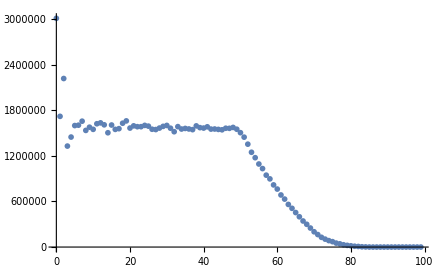

```mathematica
rdf= ReadList["~/phd-stuff/courses/astrid_sim/radialdistfunc.txt",Number,RecordLists->True];
ListPlot[rdf]
```

```mathematica
sigma=3.4*^-10;
boxlength=10.229*sigma;
```

3.47786×10^-9

6.95572×10^-10

3.01192×10^-9

3.01192×10^-9